# Straightening at a Scale

A germ is a shortest path, here of eight edges ending at the centre of the graph. We extend it forward by ten steps.

A walk is a geodesic at infra-scale r when every r+1 consecutive vertices of it form a shortest path. The observer checks straightness only within a horizon of r steps; at scale ∞ the whole walk is a shortest path.

The beam of the germ at scale r is the set of all geodesics at scale r that extend the germ. A most visited member is one that maximizes the sum of the vertex and edge densities of the beam along it.

The question: from which scale r^* on is the most visited member of the beam a segment, a shortest path between its ends? We answer it on three lattices.

The pictures keep the embedding of the substrate so that the reader sees the plane; only the chord deviation below uses it.

## Setup

```mathematica
Needs["WolframInstitute`InfraGeometry`"]
```

## The beam at a scale

Each picture is one lattice at one scale: the rows are the square, the triangular and the hexagonal tiling, the columns the scales r=2,4,8.

The beam is orange, its endpoints green, each sized by the number of members ending there. The most visited members are red, all of them; the germ is drawn last.

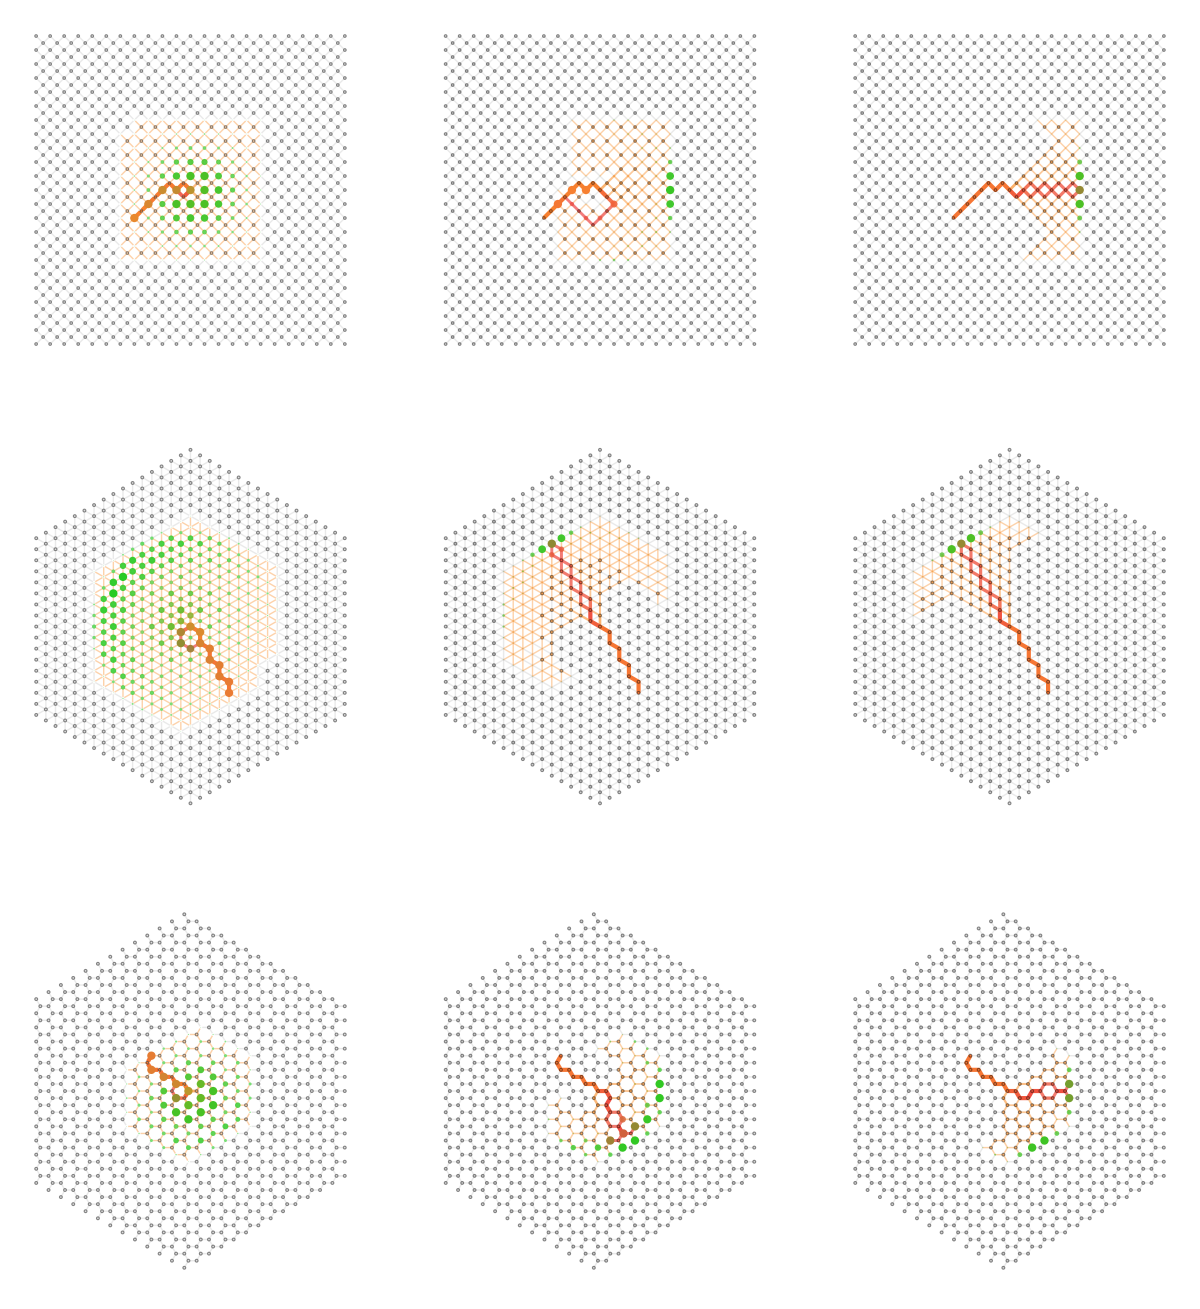

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, "Large", "KeepCoordinates" -> True])},
    {c = InfraCenter[g]},
    {germ = First @ FindInfraRepresentative[g, InfraSegment[First @ FindInfraShell[g, c, 8], c], 1]},
    {walks = FindInfraGeodesic[g, germ, r, {10}, All, "Direction" -> "Forward"]},
    InfraSubstrateHighlight[g, {
      walks -> StandardOrange,
      SelectInfraWalk[g, walks, All, "From" -> "MostVisited"] -> StandardRed,
      InfraWalk[germ] -> StandardOrange,
      Counts[Last @ Last @ Sort @ VertexList @ # & /@ walks] -> StandardGreen},
      "ThicknessRange" -> {1, 3}]],
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph"}},
  {r, {2, 4, 8}}]
```

At the smallest scale the beam fans out over a wide region and its endpoints fill it. Every member starts at the germ, so the density is highest there, and the most visited member is the one that stays near the germ: it circles around the end of the germ. A geodesic at a small scale may revisit a vertex, and these members do.

From a scale on the endpoints gather on a short arc and the most visited members run straight away from the germ. At the middle scale this has happened on the triangular tiling only; the square and the hexagonal tilings still bend.

The straight members need not continue the germ's direction: a lattice keeps a direction only up to the cone of its lattice directions.

## The scale of straightness

Two readouts of the most visited members, for every scale r=2,…,10, each the worst over the ties. The extension is a member without the germ.

The excess of an extension is its length minus the distance between its ends. It is zero exactly when the extension is a segment, so the threshold r^* is the scale where the excess first vanishes.

The chord deviation is the largest distance of the extension's vertices from the chord joining its ends, in units of the edge length, read in the plane.

```mathematica
With[
  {readouts = Table[
    With[
      {g = (SeedRandom[2]; InfraSubstrate[name, "Large", "KeepCoordinates" -> True])},
      {c = InfraCenter[g], d = GraphDistanceMatrix[g], xy = AssociationThread[VertexList[g], GraphEmbedding[g]]},
      {germ = First @ FindInfraRepresentative[g, InfraSegment[First @ FindInfraShell[g, c, 8], c], 1],
       unit = EuclideanDistance @@ Lookup[xy, List @@ First @ EdgeList @ g]},
      Table[
        With[
          {walks = FindInfraGeodesic[g, germ, r, {10}, All, "Direction" -> "Forward"]},
          {ext = Drop[Last /@ Sort @ VertexList @ #, Length[germ] - 1] & /@ SelectInfraWalk[g, walks, All, "From" -> "MostVisited"]},
          {{r, Max[Length[#] - 1 - d[[VertexIndex[g, First @ #], VertexIndex[g, Last @ #]]] & /@ ext]},
           {r, Max[Max[RegionDistance[Line[Lookup[xy, {First @ #, Last @ #}]], Lookup[xy, #]]] & /@ ext] / unit}}],
        {r, 2, 10}]],
    {name, {"SquareTilingGraph", "TriangularTilingGraph", "HexagonalTilingGraph"}}]},
  GraphicsRow[{
    ListLinePlot[readouts[[All, All, 1]], PlotRange -> All, AxesLabel -> {Text["r"], Text["excess"]},
      PlotLegends -> Text /@ {"square", "triangular", "hexagonal"}],
    ListLinePlot[readouts[[All, All, 2]], PlotRange -> All, AxesLabel -> {Text["r"], Text["deviation"]},
      PlotLegends -> Text /@ {"square", "triangular", "hexagonal"}]}]]
```

-Graphics-

Below the threshold the most visited extension is far from a segment; at the threshold the excess drops to zero and stays there. The most visited member jumps from a walk near the germ to a segment.

The triangular tiling straightens first, then the square tiling, then the hexagonal tiling.

On the square and the triangular tilings the deviation falls at the same threshold to a floor, the staircase of a segment off the lattice directions. On the hexagonal tiling it falls only a little and grows again: a straight extension zigzags almost as far from its chord as a bent one.

## Open questions

[[ The inextensible geodesic at scale r as an object: the infinite walks of the window graph from the germ's window. Is its most visited member eventually a ray at every scale above r^*, and how does r^* depend on the length of the germ? ]]

[[ The loss of direction on a lattice: the straight members follow the cone, not the germ. Does a mesh or a sprinkling, with no preferred directions, restore the germ's direction at large scales? ]]

Related Guides

EuclideanInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/EuclideanInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/StraighteningAtScaleTutorial

### Keywords

geodesic

infra-scale

germ

extension

beam

most visited

straightness

segment

tiling